## Functions used for encoding and decoding

```mathematica
updateState::usage = "Updates CA loop state based on rule";
updateState[rule_,state_]:=(
 state[[1]]->CellularAutomaton[rule,state[[2]]](*Single evolution of rule*)
)

getReading::usage = "Measures the state of a given index";
getReading[state_,readindex_]:=(
state[[2]][[readindex]]
)

getCandidates::usage = "Creates all possible candidate states that can be represented with a given number of bits";
getCandidates[datasize_]:=(
cand = Tuples[{0,1},datasize];
Thread[cand->cand])

eliminateCandidates::usage = " Eliminates candidates that do not agree with the latest reading";
eliminateCandidates[candidates_,readindex_,reading_]:=(
Select[candidates,getReading[#,readindex]==reading&]
)


updateAllCandidates::usage = "Updates all candidate states";
updateAllCandidates[rule_,candidates_]:=(
updateState[rule,#1]&/@candidates
)

stepDecoder::usage = "Does a single step of the Decoder";
stepDecoder[rule_,candidates_,readindex_,reading_]:=(
updatedcandidates = updateAllCandidates[rule,candidates];
validcandidates = eliminateCandidates[updatedcandidates,readindex,reading])

encodeMasterState::usage = "Encodes data by reading a column of CA";
encodeMasterState[rule_,masterstate_,readindex_,nupdates_]:=(
CellularAutomaton[rule,masterstate,nupdates][[;;,readindex]])

decodeNoFirstUpdate::usage = "Decodes the data, should not technically take masterstate as argument";
decodeNoFirstUpdate[rule_,encodedsequence_,datasize_,readindex_]:=(
candidates = getCandidates[datasize];
k =1;
candidates = eliminateCandidates[candidates,readindex,encodedsequence[[k]]] ;(*Edge case*)
k=k+1;
While[k≤Length[encodedsequence],
(*Print[k];*)
candidates = stepDecoder[rule,candidates,readindex,encodedsequence[[k]]];
(*Print[Length[candidates]];*)
k=k+1];
candidates)
```

Applying functions to a problem

```mathematica
rule = 60;
n = 7;
readindex = 3;
masterstate= RandomInteger[{0,1},n]
encodelength = n-2;
encodedsequence = encodeMasterState[rule,masterstate,readindex,encodelength]


decodeNoFirstUpdate[rule,encodedsequence,n,readindex]
```

{1,0,1,1,0,1,1}

{1,1,0,1,0,0}

{{1,0,1,0,0,1,1}→{1,1,0,1,0,0,1},{1,0,1,1,0,1,1}→{0,0,0,0,1,0,1}}

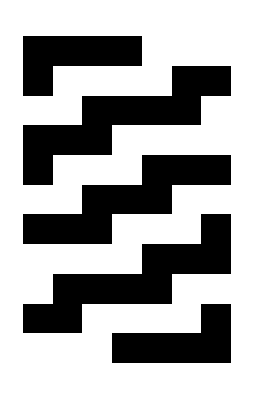

```mathematica
ArrayPlot[CellularAutomaton[15,{1,1,1,1,0,0,0},10]]
```

```mathematica
Threshold[Range[10],4]
```

{0,0,0,0,5,6,7,8,9,10}